```mathematica
AN1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/short/analytical.d0.02-2nd1.txt",{Number,Number}];
gap0=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.2e4-e6-e6-200.txt",{Number,Number}];
gap1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.5e3-e5-e5-200.txt",{Number,Number}];
gap2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.5e3-e6-e5-200.txt",{Number,Number}];
gap3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.5e3-e6-e6-200.txt",{Number,Number}];
gap4=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.5e3-e6-e7-2e2.txt",{Number,Number}];
gap5=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.5e3-e6-e8-2e2.txt",{Number,Number}];
```

```mathematica
gap6=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.e5-e7-e7-1000.txt",{Number,Number}];
gap7=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.e6-e5-e0-1.txt",{Number,Number}];
gap8=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.5e6-e6-e6-5e2.txt",{Number,Number}];
gap9=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.e7-e5-e0-1.txt",{Number,Number}];
```

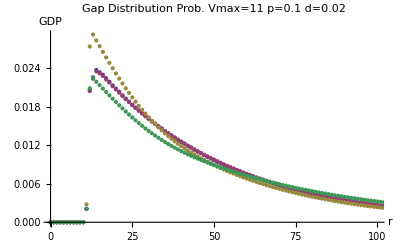

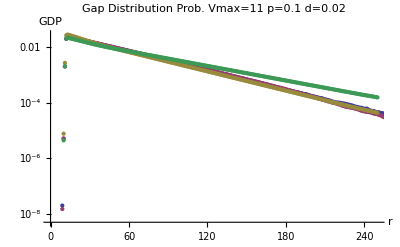

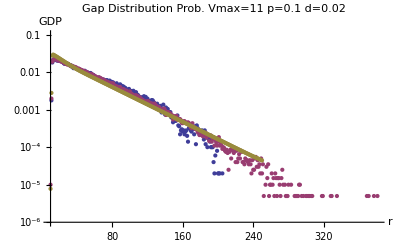

```mathematica
d="0.02";
dd=0.02;
ddd=1/(1/dd-10);
p="0.1";
vmax="11";
random=Table[{i,(1-ddd)^i*ddd},{i,0,10/ddd}];

ListPlot[{gap5,gap8,AN1,AN3},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,100},Full}]
ListLogPlot[{gap5,gap8,AN1,AN3},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,250},Full}]
ListLogPlot[{gap1,gap9,AN1},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{Full,{10^-6,0.1}}]
```

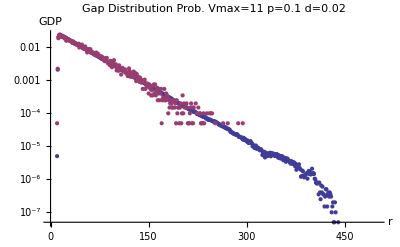

```mathematica
ListLogPlot[{gap1,gap3},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,500},Full}]
```

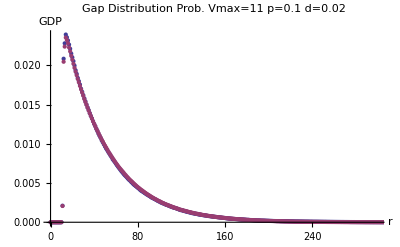

```mathematica
ListPlot[{gap1,gap5},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,300},Full}]
```

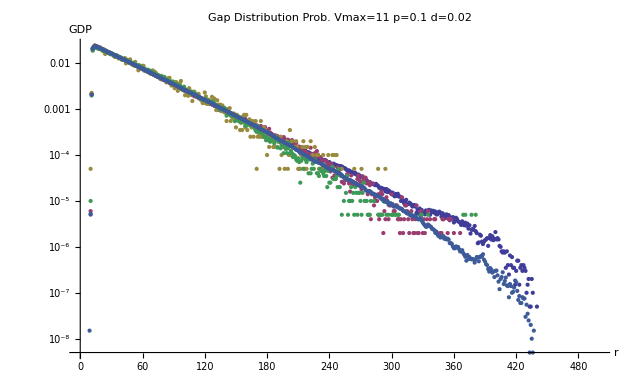

```mathematica
ListLogPlot[{gap1,gap2,gap3,gap4,gap5},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,500},Full}]
```

```mathematica
gapmax=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.5e3-e6-e7-2e2-max.txt",{Number,Number}];
```

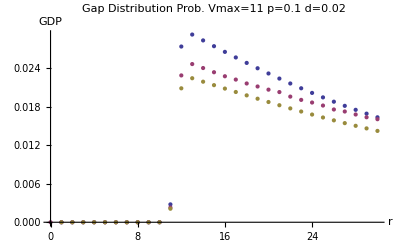

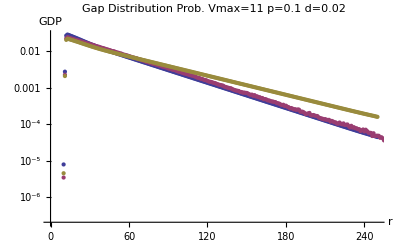

```mathematica
ListPlot[{AN1,gapmax,AN3},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,30},Full}]
ListLogPlot[{AN1,gapmax,AN3},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,250},Full}]
```

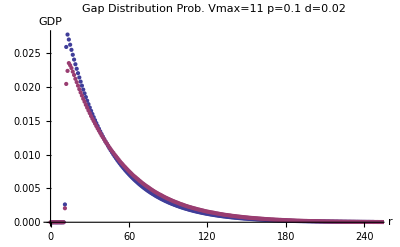

```mathematica
check=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/analytical.d0.02-check.txt",{Number,Number}];
ListPlot[{check,gap8},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,250},Full}]
```

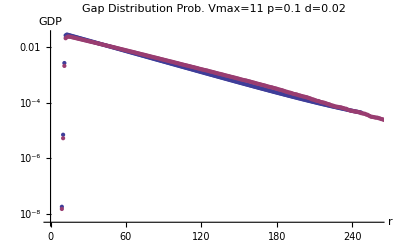

```mathematica
ListLogPlot[{check,gap8},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,260},Full}]
```

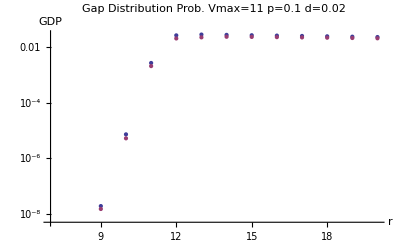

```mathematica
ListLogPlot[{check,gap8},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{7,20},Full}]
```

```mathematica
check[[245]]
gap8[[246]]
```

{245,0.0000681405}

{245,0.000044905}

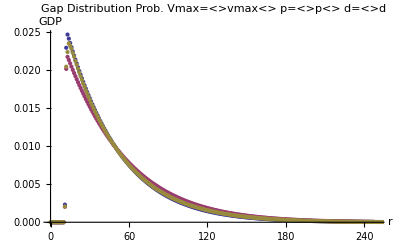

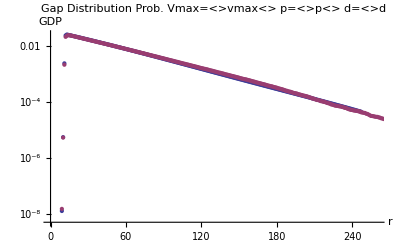

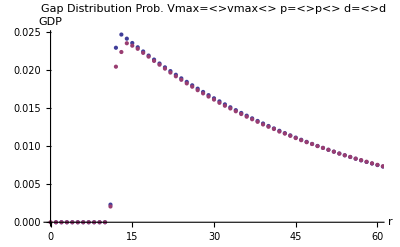

```mathematica
check2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/analytical.d0.02-check2.txt",{Number,Number}];
check1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/analytical.d0.02-check1.txt",{Number,Number}];
ListPlot[{check1,check2,gap8},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,250},Full}]
ListLogPlot[{check1,gap8},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,260},Full}]
ListPlot[{check1,gap8},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,60},Full}]
```

```mathematica
check1[[20]]
gap8[[21]]
```

{20,0.020873}

{20,0.0207174}

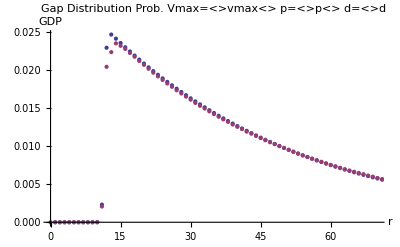

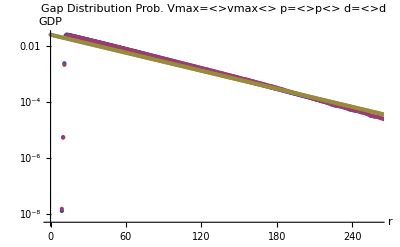

```mathematica
ddd=1/(1/dd-9);
random=Table[{i,(1-ddd)^i*ddd},{i,0,10/ddd}];
check3=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/analytical.d0.02-check3.txt",{Number,Number}];
ListPlot[{check3,gap8},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{"r",GDP}
,PlotRange->{{0,70},Full}]
ListLogPlot[{check3,gap8,random},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{"r",GDP}
,PlotRange->{{0,260},Full}]
```

```mathematica
check3[[240]]
gap8[[241]]
```

{240,0.0000536125}

{240,0.000050315}

```mathematica
c2[[240]]
r2[[241]]
```

0.0000536125

0.000050315

0.025

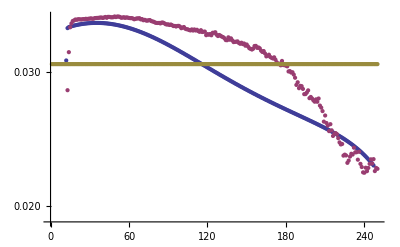

```mathematica
dd=0.02;
ddd=1/(1/dd-10)
r2=gap8[[All,2]];
c2=check3[[All,2]];
random=Table[{i,(1-ddd)^i*ddd*1.2},{i,0,10/ddd}];
rnd2=random[[All,2]];
rc=Table[{i,c2[[i]]*(1-ddd)^(-(i))},{i,0,250}];
rg=Table[{i,r2[[i]]*(1-ddd)^(-(i))},{i,1,250}];
rand=Table[{i,rnd2[[i]]*(1-ddd)^(-(i))},{i,0,250}];
ListLogPlot[{rc,rg,rand}]
```

```mathematica
gapmax=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/FFT-Analyse/bit/results/vmax11/track/GapD.d.0.02.p0.1.v11.5e4-e7-e7-e3-max.txt",{Number,Number}];
```

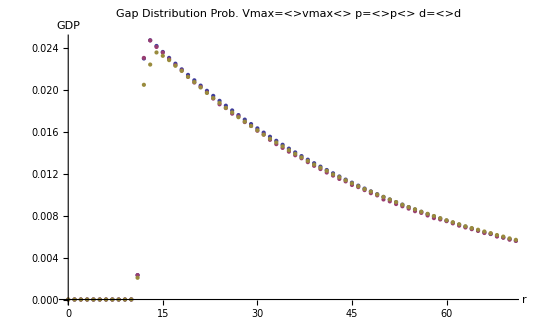

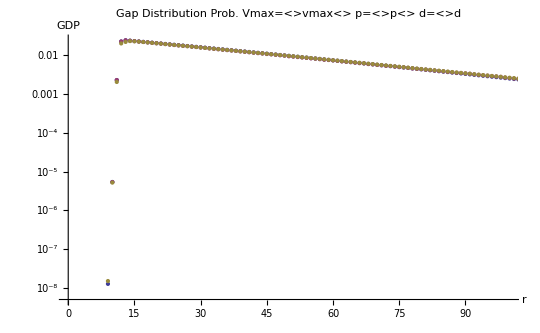

```mathematica
ListPlot[{check3,gapmax,gap8},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{"r",GDP}
,PlotRange->{{0,70},Full}]
ListLogPlot[{check3,gapmax,gap8},PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{"r",GDP}
,PlotRange->{{0,100},Full}]
```